```mathematica
Clear["Global`*"]
```

```mathematica
int1[y_,α_,x_,a_]:=2Pi((Integrate[q^2/(q^2+#1*y*q+α),q])/.q->x&@@{a})
```

```mathematica
int1[y,α,x,a];
```

```mathematica
intq[R_,y_,α_,a_]:=(int1[y,α,R,#])-(int1[y,α,0,#])&@@{a}//Simplify
```

```mathematica
int2[R_,y_,α_,a_]:=Evaluate[Integrate[intq[R,y,α,q1],q1]]/.q1->a
```

```mathematica
int2[R,y,α,1]-int2[R,y,α,-1]//Simplify//Expand;
```

```mathematica
intqθ[R_,y_,α_]:=(int2[#1,#2,#3,1])-(int2[#1,#2,#3,-1])&@@{R,y,α}//Simplify//Expand
ll[x1_,x2_,x3_]:=ll[x1,x2,x3]=Evaluate[4Pi*x1-Evaluate[intqθ[#1,#2,#3]&@@{x1,x2,x3}]//Simplify];
```

```mathematica
intqθ[R,y,α];
```

```mathematica
ll[x1,x2,x3]//FullSimplify;
```

```mathematica
L[R_,y_,α_]:=L[R,y,α]=ll[x1,x2,x3]/.{x1->R,x2->y,x3->α}
```

```mathematica
L[R,y,α]//FullSimplify
```

1/2 π (4 R+2 √(-y^2+4 α) (-ArcTan[(-2 R+y)/(√(-y^2+4 α))]+ArcTan[(2 R+y)/(√(-y^2+4 α))])+((2 R^2-y^2+2 α) (Log[R^2-R y+α]-Log[R (R+y)+α]))/y)

```mathematica
D[L[R,y,α],R]//Simplify
```

(2 π (2 y+R Log[R^2-R y+α]-R Log[R^2+R y+α]))/y

```mathematica
Manipulate[Manipulate[Plot[{Evaluate[D[L[R,y,k*y^2/4],R]]},{R,0,100}],{k,1.001,3}],{y,1,10}]
```

```mathematica
2+x*(Log[x^2-x+1.312/4]-Log[x^2+x+1.312/4])//FullSimplify
```

2+x Log[0.328+(-1+x) x]-x Log[0.328+x+x^2]

```mathematica
NSolve[{2+x*(Log[x^2-x+1/3-0.001]-Log[x^2+x+1/3-0.001])==0&&(0≤x≤100)},x]
```

{{x→4.70394}}

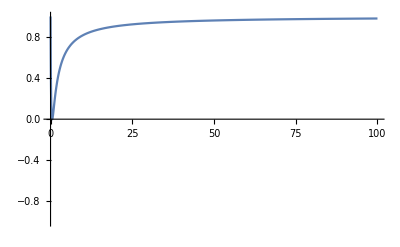

```mathematica
Plot[(x^2-x+1/4-0.001)/(x^2+x+1/4-0.001),{x,0,100},PlotRange->{{0,100},{-1,1}}]
```

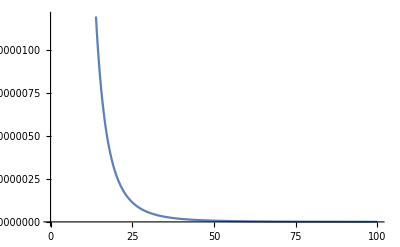

```mathematica
Plot[2-x*Log[1+(2x)/(x(x-1)+1/3)],{x,0,100}]
```

```mathematica
2-x*((2x)/(x^2-x+k))/Sqrt[((2x)/(x^2-x+k))+1]//Simplify
```

2-(2 x^2 √((k+x+x^2)/(k+(-1+x) x)))/(k+x+x^2)

```mathematica
%//FullSimplify
```

2-(2 x^2 √(1+(2 x)/(k+(-1+x) x)))/(k+x+x^2)

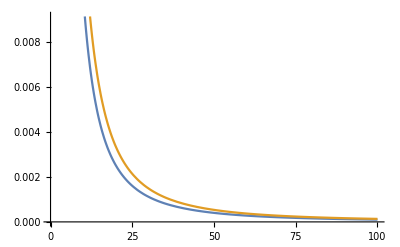

```mathematica
Plot[{2-(2 x^2 √((k+x+x^2)/(k+(-1+x) x)))/(k+x+x^2)/.k->1,2-x*Log[1+(2x)/(x(x-1)+1)]},{x,0,100}]
```

```mathematica
Solve[%==0,x]
```

{{x→-k/(√(1-2 k))},{x→k/(√(1-2 k))}}

```mathematica
{R+(-2 R^2+y^2-2 α)/(2 R),-1/2 √(-y^2+4 α) (-ArcTan[(-2 R+y)/(√(-y^2+4 α))]+ArcTan[(2 R+y)/(√(-y^2+4 α))])}/.{α->k*y^2/4}
```

{R+(-2 R^2+y^2-(k y^2)/2)/(2 R),-1/2 √(-y^2+k y^2) (-ArcTan[(-2 R+y)/(√(-y^2+k y^2))]+ArcTan[(2 R+y)/(√(-y^2+k y^2))])}

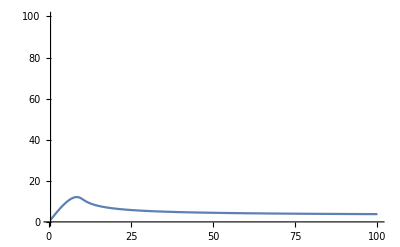

```mathematica
Plot[L[R,y,α]/.{R->x,y->19.9,α->100},{x,0.5,100},PlotRange->{{0.5,100},{0,100}}]
```

```mathematica
Manipulate[Manipulate[Manipulate[L[R,y,α]//N,{R,0,100}],{α,4y^2,1000}],{y,0,10}]
```

```mathematica
f[R_,y_,α_]:=L[#1,#2,#3]&@@{R,y,α}
```

```mathematica
f[26]
```

f[26]

```mathematica
f[x]
```

```mathematica
Manipulate[Manipulate[Plot[{L[R,y,x],Pi*Sqrt[x]},{x,y^2/4,10000000}],{R,0,1000000}],{y,1,1000}]
```

```mathematica
Manipulate[Manipulate[Plot[{L[R,y,x]},{R,0,10000},PlotRange->{{0,10000},{0,1000}}],{x,y^2/4+0.0001,1000000}],{y,1,1000}]
```

```mathematica
Manipulate[Manipulate[Plot[{L[R,y,k*y^2/4]},{R,0,100000},PlotRange->{{0,100000},{0,1000}}],{k,1.0001,4}],{y,1,1000}]
```

```mathematica
L[100000000,486,1.25*486^2/4]
```

```mathematica
FindMaximum[L[R,1,1.35*1^2/4],R]
```

{0.929296,{R→18087.9}}

```mathematica
D[L[R,y,α],R]//Simplify
```

(2 y+R Log[R^2-R y+α]-R Log[R^2+R y+α])/y

```mathematica
%//FullSimplify
```

(2 y+R Log[R^2-R y+α]-R Log[R (R+y)+α])/y

```mathematica
D[L[R,y,α],R]//FullSimplify
```

(2 y+R Log[R^2-R y+α]-R Log[R (R+y)+α])/y

```mathematica
Series[(2 y+R Log[R^2-R y+α]-R Log[R (R+y)+α])/y,{R,Infinity,2}]
```

(-(2 y^2)/3+2 α)/R^2+O[1/R]^3

```mathematica
g[R_,y_,α_]:=(2 y+R Log[R^2-R y+α]-R Log[R (R+y)+α])/y;
```

```mathematica
Manipulate[Manipulate[Plot[g[R,y,k*y^2/4],{R,1,1000}],{k,1.001,3}],{y,1,10}]
```

```mathematica
L[R,y,k*y^2/4]
```

(π (4 R y+2 y √(-y^2+k y^2) ArcTan[(2 R-y)/(√(-y^2+k y^2))]+2 y √(-y^2+k y^2) ArcTan[(2 R+y)/(√(-y^2+k y^2))]+2 R^2 Log[R^2-R y+(k y^2)/4]-y^2 Log[R^2-R y+(k y^2)/4]+1/2 k y^2 Log[R^2-R y+(k y^2)/4]-2 R^2 Log[R^2+R y+(k y^2)/4]+y^2 Log[R^2+R y+(k y^2)/4]-1/2 k y^2 Log[R^2+R y+(k y^2)/4]))/(2 y)

```mathematica
%//Simplify
```

1/(4 y)π (8 R y+4 y √((-1+k) y^2) ArcTan[(2 R-y)/(√((-1+k) y^2))]+4 y √((-1+k) y^2) ArcTan[(2 R+y)/(√((-1+k) y^2))]+4 R^2 Log[4 R^2-4 R y+k y^2]-2 y^2 Log[4 R^2-4 R y+k y^2]+k y^2 Log[4 R^2-4 R y+k y^2]-4 R^2 Log[4 R^2+4 R y+k y^2]+2 y^2 Log[4 R^2+4 R y+k y^2]-k y^2 Log[4 R^2+4 R y+k y^2])

```mathematica
%//FullSimplify
```

1/8 (8 R+4 √(-1+k) y ArcTan[(2 R-y)/(√(-1+k) y)]+4 √(-1+k) y ArcTan[(2 R+y)/(√(-1+k) y)]+((4 R^2+(-2+k) y^2) (Log[4 R^2-4 R y+k y^2]-Log[4 R^2+4 R y+k y^2]))/y)

```mathematica
Manipulate[Manipulate[Plot[{4 √(-1+k) y ArcTan[(2 R-y)/(√(-1+k) y)]+4 √(-1+k) y ArcTan[(2 R+y)/(√(-1+k) y)],-(64 ((-4+k) (-1+k)) R^3)/(3 (k^3 y^2))},{R,1,y/2}],{k,1.001,3}],{y,1,10000}]
```

```mathematica
Series[4 √(-1+k) y ArcTan[(2 R-y)/(√(-1+k) y)]+4 √(-1+k) y ArcTan[(2 R+y)/(√(-1+k) y)],{R,0,5}]
```

(16 (-1+k) R)/k-(64 ((-4+k) (-1+k)) R^3)/(3 (k^3 y^2))+(256 (-1+k) (16-12 k+k^2) R^5)/(5 k^5 y^4)+O[R]^6

```mathematica
4 √(-1+k) y (8(2 R-y)/(√(-1+k) y))/(3+Sqrt[25+256/Pi^2((2 R-y)/(√(-1+k) y))^2])+4 √(-1+k) y (8(2 R+y)/(√(-1+k) y))/(3+Sqrt[25+80/3((2 R+y)/(√(-1+k) y))^2])
```

(32 (2 R-y))/(3+√(25+(256 (2 R-y)^2)/((-1+k) π^2 y^2)))+(32 (2 R+y))/(3+√(25+(80 (2 R+y)^2)/(3 (-1+k) y^2)))

```mathematica
%//FullSimplify
```

(32 (2 R-y))/(3+√(25+(256 (-2 R+y)^2)/((-1+k) π^2 y^2)))+(32 (2 R+y))/(3+√(25+(80 (2 R+y)^2)/(3 (-1+k) y^2)))

```mathematica
Manipulate[Manipulate[Plot[{2Pi(4 √(-1+k) y ArcTan[(2 R-y)/(√(-1+k) y)]+4 √(-1+k) y ArcTan[(2 R+y)/(√(-1+k) y)]),2Pi(16/(1+1/(-1+k))R),8Pi*R,8L[R,y,k*y^2/4],2Pi*8*1/4 (4+4 √(-1+k) ArcTan[2/(√(-1+k))]+(-1+k) Log[-1+k]-(-1+k) Log[3+k])*R},{R,0,y/2}],{k,1.34,3}],{y,10,10000}]
```

```mathematica
L[10/2,10,k*10^2/4]/5//FullSimplify
```

1/2 π (4+4 √(-1+k) ArcTan[2/(√(-1+k))]+(-1+k) Log[-1+k]-(-1+k) Log[3+k])

```mathematica
Series[%,{k,4/3,1}]
```

(2 π+(2 π ArcTan[2 √3])/(√3)-1/6 π Log[13])+(√3 π ArcTan[2 √3]-1/2 π Log[13]) (k-4/3)+O[k-4/3]^2

```mathematica
%//N
```

9.61892+2.98909 (k-1.33333)+O[k-1.33333]^2

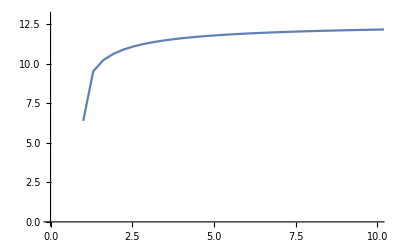

```mathematica
Plot[%,{k,1.0001,1000},PlotRange->{{0,10},{0,13}}]
```

```mathematica
%//N
```

12.5663

```mathematica
4Pi//N
```

12.5664

```mathematica
L[R,y,α]
```

(π (4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α]))/(2 y)

```mathematica
%//FullSimplify
```

1/2 π (4 R+2 √(-y^2+4 α) (-ArcTan[(-2 R+y)/(√(-y^2+4 α))]+ArcTan[(2 R+y)/(√(-y^2+4 α))])+((2 R^2-y^2+2 α) (Log[R^2-R y+α]-Log[R (R+y)+α]))/y)

```mathematica
Series[%,{y,0,1}]
```

4 π √α ArcTan[R/(√α)]+O[y]^2

```mathematica
%//FullSimplify
```

1/4 (4+4 √(-1+k) ArcTan[2/(√(-1+k))]+(-1+k) Log[-1+k]-(-1+k) Log[3+k])

```mathematica
%/.k->γ
```

1/4 (4+4 √(-1+γ) ArcTan[2/(√(-1+γ))]+(-1+γ) Log[-1+γ]-(-1+γ) Log[3+γ])

```mathematica
%//TeXForm
```

\frac{1}{4} \left((\gamma -1) \log (\gamma -1)-(\gamma -1) \log (\gamma +3)+4 \sqrt{\gamma -1} \tan ^{-1}\left(\frac{2}{\sqrt{\gamma -1}}\right)+4\right)

```mathematica
%//N
```

0.25 (4.+4. √(-1.+k) ArcTan[2./(√(-1.+k))]+(-1.+k) Log[-1.+k]-1. (-1.+k) Log[3.+k])

```mathematica
Solve[x^2+x-2==0,x]
```

{{x→-2},{x→1}}

```mathematica
D[D[L[R,y,α],R],R]
```

1/(4 y)(-(2 R^2 (2 R-y)^2)/((R^2-R y+α)^2)+((2 R-y)^2 y^2)/((R^2-R y+α)^2)-(2 (2 R-y)^2 α)/((R^2-R y+α)^2)+(4 R^2)/(R^2-R y+α)+(8 R (2 R-y))/(R^2-R y+α)-(2 y^2)/(R^2-R y+α)+(4 α)/(R^2-R y+α)+(2 R^2 (2 R+y)^2)/((R^2+R y+α)^2)-(y^2 (2 R+y)^2)/((R^2+R y+α)^2)+(2 (2 R+y)^2 α)/((R^2+R y+α)^2)-(4 R^2)/(R^2+R y+α)+(2 y^2)/(R^2+R y+α)-(8 R (2 R+y))/(R^2+R y+α)-(4 α)/(R^2+R y+α)-(16 (2 R-y) y)/((-y^2+4 α) (1+(2 R-y)^2/(-y^2+4 α))^2)-(16 y (2 R+y))/((-y^2+4 α) (1+(2 R+y)^2/(-y^2+4 α))^2)+4 Log[R^2-R y+α]-4 Log[R^2+R y+α])

```mathematica
%//FullSimplify
```

```mathematica
(2 R (R^2-α))/((R^2-R y+α) (R (R+y)+α))+(Log[R^2-R y+α]-Log[R (R+y)+α])/y//TeXForm
```

\frac{2 R \left(R^2-\alpha \right)}{\left(\alpha +R^2-R y\right) (\alpha +R (R+y))}+\frac{\log \left(\alpha +R^2-R y\right)-\log (\alpha +R (R+y))}{y}

```mathematica
Manipulate[Manipulate[Plot[{(2 R (R^2-k*y^2/4))/((R^2-R y+k*y^2/4) (R (R+y)+k*y^2/4))+(Log[R^2-R y+k*y^2/4]-Log[R (R+y)+k*y^2/4])/y,(2 R (R^2-k*y^2/4))/((R^2-R y+k*y^2/4) (R (R+y)+k*y^2/4))-(2(2R*y)/(R^2-R y+k*y^2/4))/(2+(2R*y)/(R^2-R y+k*y^2/4))1/y},{R,0,1000},PlotRange->{{0,y/2+0.001},{-1,1}}],{k,1.0001,3}],{y,10,100}]
```